```mathematica
doyle[pi_,qi_]:=Module[{p=pi,q=qi,s,t,r},r[s_,t_,p_,q_]:=(s^2+s^(2 p/q)-2 s^((p+q)/q) Cos[(2 π+p t-q t)/q])/(s+s^(p/q))^2;
{s,t}={s,t}/.FindRoot[{r[s,t,0,1]-r[s,t,p,q]==0,r[s,t,0,1]-r[s^(p/q),(p*t+2. Pi)/q,0,1]==0},{{s,1.5},{t,0}}];
{s*Exp[I*t],s^(p/q)*Exp[I (p*t+2*Pi)/q],Sqrt[r[s,t,0,1]]}]

{a,b,r}=doyle[2,12]
```

{1.67036+0.343254 ⅈ,0.927594+0.578172 ⅈ,0.278395}

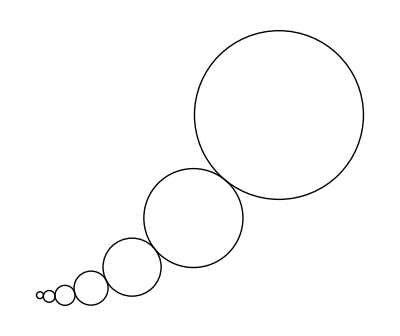

```mathematica
iterate[a_,b_,j_,n_]:=Module[{start=b^j},Table[a^i*start,{i,Range[-n,n]}]]
Graphics[Circle[ReIm[#],r*Abs[#]]&/@iterate[a,b,0,3]]
```

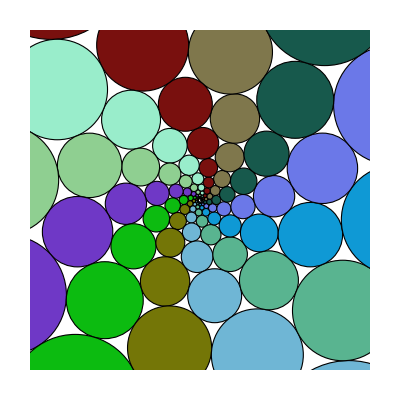

```mathematica
toCirle[z_,r_]:=Disk[{Re[z],Im[z]},Abs[z]*r];
pack=Table[iterate[a,b,j,5],{j,12}];
gr=Graphics[{EdgeForm[Black],Map[{RandomColor[],toCirle[#,r]&/@#}&,pack]},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[Black],FaceForm[Gray],Table[toCirle[a^i*b^j,r],{i,i1,i2},{j,j1,j2}]},PlotRange->{{-10,10},{-10,10}}],{{i1,0},-5,3,1},{{i2,0},i1,5,1},{{j1,0},-5,3,1},{{j2,0},j1,5,1}]
```

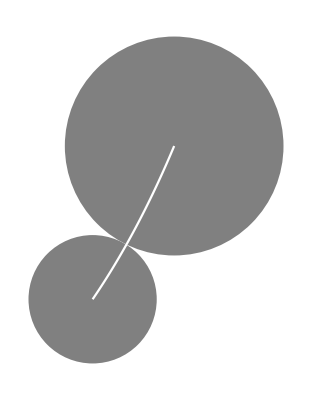

```mathematica
Show[Graphics[{FaceForm[Gray],toCirle[#,r]&/@{a^3,a^4}}],ParametricPlot[ReIm[a^3*a^t],{t,0,1},PlotStyle->White]]
```

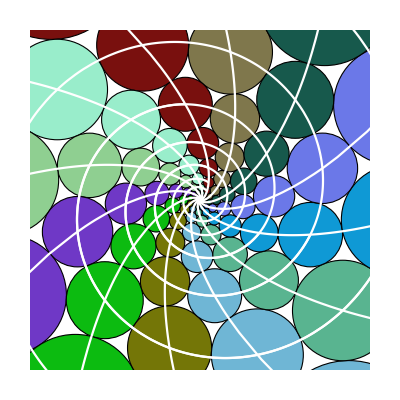

```mathematica
Show[gr,ParametricPlot[Table[ReIm[b^i a^t],{i,12}],{t,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->White],ParametricPlot[Table[ReIm[a^j b^t],{j,5}],{t,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->White]]
```

```mathematica
tb=t/.FindRoot[Abs[1-a^t]-r,{t,#}]&/@{-1/3,1/3}
```

{-0.565183,0.433533}

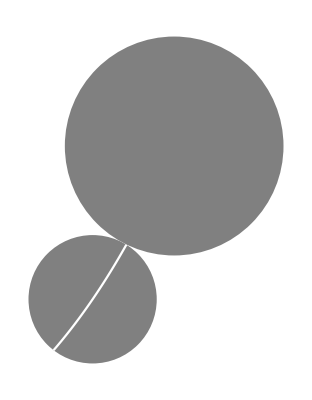

```mathematica
Show[Graphics[{FaceForm[Gray],toCirle[#,r]&/@{a^3,a^4}}],ParametricPlot[ReIm[a^3*a^t],{t,tb[[1]],tb[[2]]},PlotStyle->White]]
```

```mathematica
spoints={a*b^-1,a,b}
```

{1.46301-0.54185 ⅈ,1.67036+0.343254 ⅈ,0.927594+0.578172 ⅈ}

```mathematica
spiral[pt_]:=Module[{t1,t2},{t1,t2}=Block[{t},t/.FindRoot[Abs[1-pt^(t)]-r,{t,#}]&/@{-1/3,1/3}];
{t1,t2,Function[{i,j,t},a^i*b^j*pt^t]}]
```

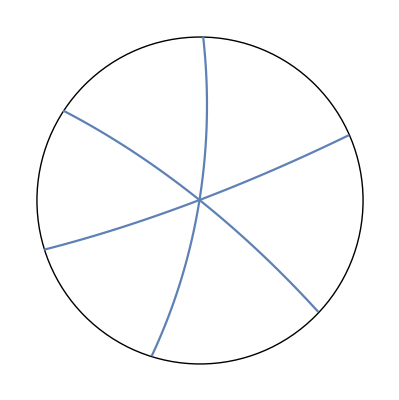

```mathematica
Show[{Graphics[Circle[{1,0},r]],ParametricPlot[ReIm@#3[0,0,t],{t,#1,#2}]&@@@spiral/@spoints}]
```

```mathematica
circle[z1_,z2_,cent_]:=Module[{zz1=z1-cent,zz2=z2-cent,r},r=Abs[Mean[{zz1,zz2}]];
#+cent&/@Nest[Riffle[#,Function[zz,With[{m=Mean[zz]},m/Abs[m]*Abs[zz1]]]/@Partition[#,2,1]]&,{zz1,zz2},5]]
```

```mathematica
createCircleParts[spirals_,i_,j_]:=Module[{center,outward,inward},outward=Table[#3[i,j,t],{t,0,#2,#2/10.}]&@@@spirals;
inward=Table[#3[i,j,t],{t,0,#1,#1/10.}]&@@@spirals;
center=a^i*b^j;
{i,j,Join[#1[[;;-2]],circle[#1[[-1]],#2[[-1]],center],Reverse[#2[[;;-2]]]]&@@@Partition[Join[outward,inward,{First[outward]}],2,1]}]
```

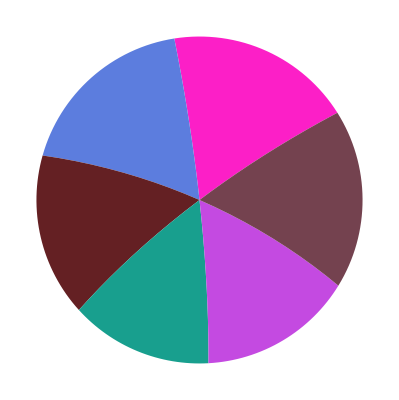

```mathematica
Graphics[{RandomColor[],Polygon[ReIm[#]]}&/@Last@createCircleParts[spiral/@spoints,1,2]]
```

```mathematica
cols={Black,RGBColor[0.078,0.71,0.964],Orange,Red,Darker@Green,Purple};
colorCircleParts[{i_,j_,parts_},col_List]:=Table[{col[[Mod[i+j+n,Length[col]]+1]],Polygon[ReIm@parts[[n]]]},{n,Length[parts]}]
```

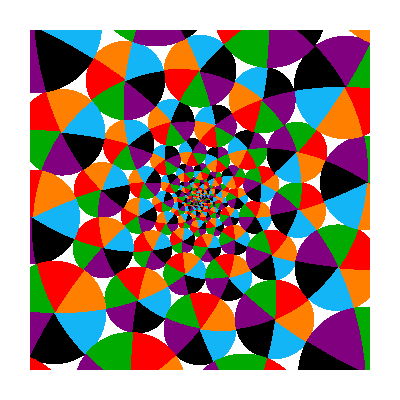

```mathematica
all=Table[colorCircleParts[createCircleParts[spiral/@spoints,i,j],cols],{i,-5,6},{j,0,12}];
Graphics[all,PlotRange->{{-20,20},{-20,20}}]
```

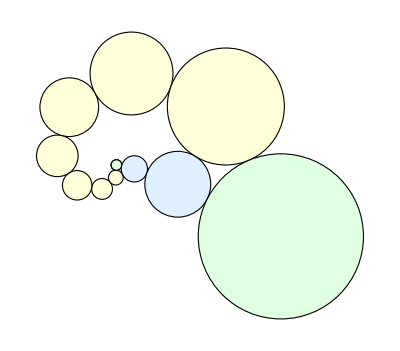

```mathematica
pqPlot[p_,q_]:=Module[{a,b,r,c1,c2},{a,b,r}=doyle[p,q];
{a,b}=Conjugate/@{a,b};
c1=toCirle[#,r]&/@NestList[a*#&,1,p-1];
c2=toCirle[#,r]&/@NestList[b*#&,1,q-1];
Graphics[{EdgeForm[Black],FaceForm[LightYellow],c2,FaceForm[LightBlue],c1,FaceForm[LightGreen],EdgeForm[Thick],toCirle[1,r],toCirle[a^p,r]}]]

pqPlot[3,8]
```

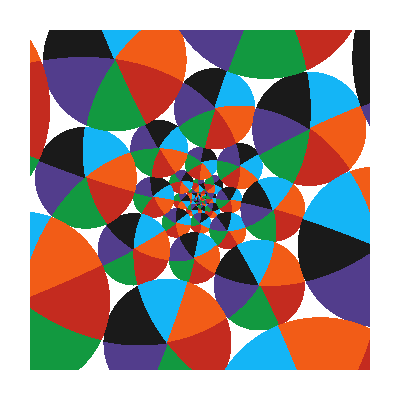

```mathematica
{a,b,r}=doyle[3,8];
{a,b}=Conjugate/@{a,b};
spoints={a*b^-1,a,b};
cols={GrayLevel[0.1],RGBColor[0.078,0.71,0.964],RGBColor[0.95,0.36,0.09],RGBColor[0.77,0.17,0.12],RGBColor[0.07,0.6,0.25],RGBColor[.32,.24,.55]};
range=5.585;

Graphics[Table[colorCircleParts[createCircleParts[spiral/@spoints,i,j],cols],{i,-5,2},{j,0,7}],PlotRange->{{-range,range},{-range,range}}]
```

```mathematica
AbsoluteTiming[doyleSpiralImages=Flatten@Table[(lcols=RandomSample[cols];
all=Table[colorCircleParts[createCircleParts[spiral/@spoints,i,j],lcols],{i,-5,6},{j,0,12}];
Image[Graphics[all,PlotRange->{{-20,20},{-20,20}}]]),{20}];]
doyleSpiralImagesBW=ColorConvert[#,"Grayscale"]&/@doyleSpiralImages;
doyleSpiralImagesBWBin=Flatten@Table[Binarize[#,b]&/@doyleSpiralImagesBW,{b,{0.15,0.45}}];

(*{31.5697,Null}*)

AbsoluteTiming[nc=16;
directBlendingImages=Table[ImageAdjust[Blend[Colorize[#,ColorFunction->RandomChoice[{"BrightBands","FruitPunchColors","AvocadoColors"}]]&/@RandomChoice[doyleSpiralImagesBWBin,nc],RandomReal[1,nc]]],{25}];]

(*{42.7025,Null}*)

Multicolumn[ColorNegate/@directBlendingImages,6]
```

{28.9707,Null}

{50.4104,Null}

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |